```mathematica
SetDirectory["C:\\Users\\olbrich\\Dropbox\\dimensionality\\QuantBeh2015-code"]
```

C:\Users\olbrich\Dropbox\dimensionality\QuantBeh2015-code

```mathematica
<< ComplexityDecomposition`
```

SetOptions::optnf: PlotTheme is not a known option for Plot.

SetOptions::optnf: PlotTheme is not a known option for ListPlot3D.

SetOptions::optnf: PlotTheme is not a known option for ListLogLinearPlot.

General::stop: Further output of SetOptions :: optnf will be suppressed during this calculation.

Part::span: 1 ;; {-1, 0, -1, -1} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: {1, 2, 1, 1} ;; All is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: {1 - Span ;; 1 ;; Span ;; Span, 2 - Span ;; 1 ;; Span ;; Span, 1 - Span ;; 1 ;; Span ;; Span, 1 - Span ;; 1 ;; Span ;; Span} ;; {-1 + {0, 1, 0, 0} ⟦ {1, 2, 1, 1} ;; All ⟧, {0, 1, 0, 0} ⟦ {1, 2, 1, 1} ;; All ⟧, -1 + {0, 1, 0, 0} ⟦ {1, 2, 1, 1} ;; All ⟧, -1 + {0, 1, 0, 0} ⟦ {1, 2, 1, 1} ;; All ⟧} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part :: span will be suppressed during this calculation.

Part::pspec: Part specification {0, 0.1, 0.2, 0} is neither an integer nor a list of integers.

Part::pspec: Part specification {0.4, 0.6, 0, 0} is neither an integer nor a list of integers.

Part::pspec: Part specification {0.2, 0.4, 0.2, 0.2} is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

```mathematica
TiseanExportDir="graphics/";
```

```mathematica
MIExportDir="graphics/";
```

```mathematica
CalcImgSize[1]
```

```mathematica
DecomposePlotSize=CalcImgSize[0.5];
```

## Lorenz

```mathematica
MyPlotOpts={PlotLabel->None,ImageSize->CalcImgSize[0.3]};
```

### D2 - delay 10

```mathematica
files=GetFiles["tisean/lorenz/","lorenz_d10.d2"]
basename="lorenz";
{plots,tiseandat}=TiseanD2PlotsAndData[files[[1]],1,ShowEntropy->True,EpsRange->{0.005,Infinity},PlotRange->All];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,15]
dfit =FitWithAutoCutOff[("D" /.tiseandat)[[{-1,-2,-3}]],ConstFitFun,0.0005]
ratio=GetPlotCoordinateRatio[Show[plots[[3]],PlotRange->{All,{0,14}}]];
plots4Export=
{ Show[plots[[1]],PlotFitInLog[dfit][[1]],PlotRange->{All,{0,9}},Evaluate@MyPlotOpts,Epilog->PlotFitInLog[dfit, ShowLabel->False,LabelPosition->{Automatic,-1.0}][[2]]],
Show[plots[[2]],PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->1][[1]]&,eeFits],PlotRange->{All,{0,14}},Evaluate@MyPlotOpts,Epilog->Map[PlotFitInLog[#, LabelAngle->Automatic,BasePlotRatio->ratio, LabelPosition->{.5,-0.3}][[2]]&,eeFits],PlotRangeClipping->False]}
```

```mathematica
tickopts=ReplacePart[Ticks /. AbsoluteOptions[plots[[1]]],{2->{1.8,2,2.2}}];
inset=Show[plots[[1]],ImageSize->CalcImgSize[.18],PlotLabel->None, AxesLabel->None,PlotRange->{{Log[0.01],Log[1.5]},{1.8,2.3}},LabelStyle->Directive[FontFamily->Times,FontSize->7],
GridLines->{None,{2,4,6}}, AxesOrigin->{Log[0.01],1.8}, Ticks->tickopts,Background->GrayLevel[.98],AspectRatio->0.5,Epilog->{{Dotted,AbsoluteThickness[1], Line[{{Log[0.01],2.06},{Log[50],2.06}}]},Inset[StyleLabel[2.06],{Log[0.1],2.06},{0,-1.5}]}];
```

```mathematica
d2PlotModified=Show[plots4Export[[1]],Epilog->{PlotFitInLog[dfit,ShowLabel->False,LabelPosition->{Automatic,-1}][[2]],
Inset[inset,ImageScaled[{.6,.6}],Automatic]}]
```

```mathematica
Export[TiseanExportDir<>basename<>"_D2.pdf",d2PlotModified,Background->None]
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_h2.pdf","_excess_entropy.pdf"},plots4Export[[2;;]]]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.07, DeterminismThreshold->0.5,RemoveNegative->True,ShowNegative->True,  ReplaceEndByFits->True, YPlotRangeMax->15, UseLargerRangePlateaus->True, ImageSize->DecomposePlotSize];
EEdecompPlot
```

```mathematica
"legend"/.aux
Export[TiseanExportDir<>"excess-entropy-decomp-legend_with_raw.pdf","legend"/.aux,Background->None]
```

```mathematica
detInts={{Interval[{0.01,.3}],-1,1}};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,(*Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],*)Epilog->{Gray,Map[PlotFitInLog[#,LabelSize->8,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->False][[2]]&,eeFits],Black,Map[AvgDecompInPlot@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits.pdf",Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)],Joined->True,PlotRange->All,PlotStyle->Cyan]],Background->None,ImageSize->1600];
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

### Noisy Lorenz delay 10

#### 0.005

```mathematica
basename="lorenz_noise0-005";
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/lorenz/"<>basename<>"_d10.d2",1,ShowEntropy->True, EpsRange->{0.005,Infinity},PlotRange->All];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,15]
eeFitsConst ={{LinearFitWithAutoCutOff[("E" /.tiseandat)[[{1}]],0,x,0.01],-1},{LinearFitWithAutoCutOff[("E" /.tiseandat)[[{2}]],0,x,0.01,{0,0.1}],1}}
(*dfit =LinearFitWithAutoCutOff[("D" /.tiseandat)[[{-1,-2,-3,-4}]],0,x,0.01]*)
ratio=GetPlotCoordinateRatio[Show[plots[[3]],PlotRange->{All,{0,14}}]];
plots4Export=
{ Show[plots[[1]](*,PlotFitInLog[dfit][[1]]*),PlotRange->{All,{0,9}},Evaluate@MyPlotOpts(*,Epilog->PlotFitInLog[dfit, LabelPosition->{Automatic,-1.0}][[2]]*)],
Show[plots[[2]],PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->1][[1]]&,eeFits],Map[PlotFitInLog[#[[1]]][[1]]&,eeFitsConst],PlotRange->{All,{0,14}},Evaluate@MyPlotOpts,Epilog->{Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio][[2]]&,eeFits],Map[PlotFitInLog[#[[1]],LabelPosition->{Automatic,#[[2]]}][[2]]&,eeFitsConst]},PlotRangeClipping->False]}
```

```mathematica
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_D2.pdf","_h2.pdf","_excess_entropy.pdf"},plots4Export]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.1, DeterminismThreshold->0.5,RemoveNegative->True,ShowNegative->True,  ReplaceEndByFits->True, YPlotRangeMax->14.5, UseLargerRangePlateaus->True, ImageSize->DecomposePlotSize];
EEdecompPlot
```

```mathematica
detInts={{Interval[{0.12,0.5}],-1,1}(*,{Interval[{0.7,5}],1,1}*)};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],Epilog->{Gray,Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->False][[2]]&,eeFits],Black,Map[AvgDecompInPlot[##,LabelSize->8]&@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits.pdf",Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)],Joined->True,PlotRange->All,PlotStyle->Cyan]],Background->None,ImageSize->1600];
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

deltaH plot with fits

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10,ShowLabel->False,ShowFitLines->All];
```

```mathematica
deltahfitplot=Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)[[1;;3]]],Joined->True,PlotRange->All,PlotStyle->Map[Directive[Dashed,Darker[#]]&,ColorsFromScheme[10,"Rainbow"]]],ImageSize->CalcImgSize[0.5]]
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits-demo.pdf",deltahfitplot,Background->None]
```

```mathematica
allfits=FitShortRegions[dat[[1]],LogLinFitFun,10];
allfiterrors=Map[Total[(#["FitResiduals"])^2]&, allfits[[All,1]]];
tresh=Quantile[allfiterrors,.25]
tresh2=Quantile[allfiterrors,.25]+.1StandardDeviation[allfiterrors]
Max[allfiterrors]
fitqualplot=ListLinePlot[Sort[allfiterrors],PlotRange->{Automatic,{0,0.0025}},PlotStyle->Darker[Blue],AxesLabel->{i,q[Subscript[r, i]]},AspectRatio->1,ImageSize->CalcImgSize[0.3],Prolog->{Dotted,Line[{{0,tresh},{1000,tresh}}],Dashed,Red,Line[{{0,tresh2},{1000,tresh2}}]}]
```

```mathematica
Export[TiseanExportDir<>basename<>"_fit-qualities.pdf",fitqualplot,Background->None]
```

#### 0.01

```mathematica
basename="lorenz_noise0-01";
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/lorenz/"<>basename<>"_d10.d2",1,Thresh->2.5, ShowEntropy->True, EpsRange->{0.005,Infinity},PlotRange->All];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,15]
eeFitsConst ={{LinearFitWithAutoCutOff[("E" /.tiseandat)[[{1}]],0,x,0.01],-1},{LinearFitWithAutoCutOff[("E" /.tiseandat)[[{2}]],0,x,0.01,{0.006,0.1}],1}}
ratio=GetPlotCoordinateRatio[Show[plots[[3]],PlotRange->{Automatic,{0,14}}]];
plots4Export=
{ Show[plots[[1]],PlotRange->{All,{0,9}},Evaluate@MyPlotOpts],
Show[plots[[2]],PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->1][[1]]&,eeFits],Map[PlotFitInLog[#[[1]]][[1]]&,eeFitsConst],PlotRange->{Automatic,{0,14}},Evaluate@MyPlotOpts,Epilog->{Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio][[2]]&,eeFits],Map[PlotFitInLog[#[[1]],LabelPosition->{Automatic,#[[2]]}][[2]]&,eeFitsConst]},PlotRangeClipping->False]
}
```

```mathematica
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_D2.pdf","_h2.pdf","_excess_entropy.pdf"},plots4Export]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.1, DeterminismThreshold->0.5,RemoveNegative->True,ShowNegative->True,  ReplaceEndByFits->True,YPlotRangeMax->14.5, ImageSize->DecomposePlotSize];
EEdecompPlot
```

```mathematica
detInts={{Interval[{0.15,0.5}],-1,1}};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],Epilog->{Gray,Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->False][[2]]&,eeFits],Black,Map[AvgDecompInPlot[##,LabelSize->8]&@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

#### 0.02

```mathematica
basename="lorenz_noise0-02";
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/lorenz/"<>basename<>"_d10.d2",1,ShowEntropy->True,Thresh->3, EpsRange->{0.005,Infinity},PlotRange->All];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,15]
eeFitsConst ={{LinearFitWithAutoCutOff[("E" /.tiseandat)[[{1}]],0,x,0.01],-1},{LinearFitWithAutoCutOff[("E" /.tiseandat)[[{2}]],0,x,0.01,{0.006,0.1}],.6}}
ratio=GetPlotCoordinateRatio[Show[plots[[3]],PlotRange->{{Log[0.004],All},{0,14}}]];
plots4Export=
{ Show[plots[[1]],PlotRange->{All,{0,9}},Evaluate@MyPlotOpts],
Show[plots[[2]],PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->1][[1]]&,eeFits],Map[PlotFitInLog[#[[1]]][[1]]&,eeFitsConst],PlotRange->{{Log[0.004],All},{0,14}},Evaluate@MyPlotOpts,Epilog->{Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio][[2]]&,eeFits],Map[PlotFitInLog[#[[1]],LabelPosition->{Automatic,#[[2]]}][[2]]&,eeFitsConst]},PlotRangeClipping->False]
}
```

```mathematica
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_D2.pdf","_h2.pdf","_excess_entropy.pdf"},plots4Export]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.1, DeterminismThreshold->0.5,RemoveNegative->False,ShowNegative->True,  ReplaceEndByFits->True, YPlotRangeMax->14.5, ImageSize->DecomposePlotSize];
(*EEdecompPlot*)
```

```mathematica
detInts={{Interval[{0.25,2}],-1,.7}};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],Epilog->{Gray,Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->False][[2]]&,eeFits],Black,Map[AvgDecompInPlot[##,LabelSize->7]&@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits.pdf",Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)],Joined->True,PlotRange->All,PlotStyle->Cyan]],Background->None,ImageSize->1600];
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

#### 0.01 times 10

```mathematica
basename="lorenz_noise0-01_f10";
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/lorenz/"<>basename<>"_d10.d2",1,Thresh->2.5, ShowEntropy->True, EpsRange->{0.005,Infinity},PlotRange->All];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,15]
eeFitsConst ={{LinearFitWithAutoCutOff[("E" /.tiseandat)[[{1}]],0,x,0.01],-1},{LinearFitWithAutoCutOff[("E" /.tiseandat)[[{2}]],0,x,0.01,{0.006,1}],1}}
ratio=GetPlotCoordinateRatio[Show[plots[[3]],PlotRange->{Automatic,{0,14}}]];
plots4Export=
{ Show[plots[[1]],PlotRange->{All,{0,9}},Evaluate@MyPlotOpts],
Show[plots[[2]],PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->1][[1]]&,eeFits],Map[PlotFitInLog[#[[1]]][[1]]&,eeFitsConst],PlotRange->{Automatic,{0,14}},Evaluate@MyPlotOpts,Epilog->{Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio][[2]]&,eeFits],Map[PlotFitInLog[#[[1]],LabelPosition->{Automatic,#[[2]]}][[2]]&,eeFitsConst]},PlotRangeClipping->False]
}
```

```mathematica
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_D2.pdf","_h2.pdf","_excess_entropy.pdf"},plots4Export]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.1, DeterminismThreshold->0.5,RemoveNegative->True,ShowNegative->True,  ReplaceEndByFits->True,YPlotRangeMax->14.5, ImageSize->DecomposePlotSize];
EEdecompPlot
```

```mathematica
detInts={{Interval[10 {0.2,0.5}],-1,1}};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],Epilog->{Gray,Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->False][[2]]&,eeFits],Black,Map[AvgDecompInPlot[##,LabelSize->8]&@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits.pdf",Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)],Joined->True,PlotRange->All,PlotStyle->Cyan]],Background->None,ImageSize->1600];
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

```mathematica
legend10=TiseanLegend[10]
```

```mathematica
Export[TiseanExportDir<> "legend10.pdf",legend10,Background->None]
```

### KSG Algorithm Lorenz delay 10

```mathematica
fs={"MIxnyn/lorenz/lorenzk20_d10.pi.grouped"};
plsmiar1=Map[PlotMIScan[#[[1]],#[[2]]]&,Zip[Map[Import,fs],fs]];
```

```mathematica
Show[plsmiar1[[1]],
LogLinearPlot[Const-Dim Log[x]/.{Dim->1.8,Const->4.4},{x,0.02,20},PlotStyle->fittedLineStyle],
ImageSize->200,
PlotLabel->None,Epilog->Inset[Rotate[StyleLabel[4.4-1.8 Log[ϵ]],-45Degree],{Log[12],2},{Right,Bottom}]]
```

```mathematica
Export[MIExportDir<>"lorenzk20_d10.pdf",%,Background->None];
```

```mathematica
pl2=PlotMIScan[Import["MIxnyn/lorenz/lorenznoise0-01k20_d10.pi.grouped"],"Noisy Lorenz delay=10 k=20"]
```

```mathematica
Show[pl2,
LogLinearPlot[Const-Dim Log[x]/.{Dim->0,Const->1.15},{x,0.001,3},PlotStyle->fittedLineStyle],
LogLinearPlot[Const-Dim Log[x]/.{Dim->0,Const->6.35},{x,0.001,.4},PlotStyle->fittedLineStyle],
LogLinearPlot[Const-Dim Log[x]/.{Dim->1.6,Const->4.3},{x,0.15,20},PlotStyle->fittedLineStyle],
ImageSize->200,PlotRange->{Automatic,{0,8}},
PlotLabel->None,Epilog->{Inset[Rotate[StyleLabel[4.3-1.6 Log[ϵ]],-50Degree],{Log[30],1.5},{Right,Bottom}],
Inset[StyleLabel["1.15"],{Log[0.01],1.15},{Center,Bottom}],Inset[StyleLabel["6.35"],{Log[0.01],6.1},{Center,Top}]}]
```

```mathematica
Export[MIExportDir<>"lorenz_noise0-01k20_d10.pdf",%,Background->None];
```

```mathematica
legend6=TiseanLegend[6,False]
Export[TiseanExportDir<> "legend6-1.pdf",legend6,Background->None]
```

## Snake

```mathematica
files=GetFiles["tisean/snake/","Snake*_x8_*.d2"]
MyPlotOpts={PlotLabel->None,ImageSize->CalcImgSize[0.4]};
```

### winding-bend

```mathematica
basename="Snake8_winding_bend";
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/snake/"<>basename<>"_x8_e19.d2",1,Thresh->5,PlotRange->All,EpsRange->{0.0003,Infinity}];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,15]
ratio=GetPlotCoordinateRatio[plots[[3]]];
plots4Export=
{ Show[plots[[1]],PlotRange->{All,{0,6}},Evaluate@MyPlotOpts],
Show[plots[[2]],PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->1][[1]]&,eeFits],Evaluate@MyPlotOpts,Epilog->Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->True][[2]]&,eeFits],PlotRangeClipping->True]}
```

```mathematica
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_D2.pdf","_h2.pdf","_excess_entropy.pdf"},plots4Export]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10,FitQualityQuantile->0.5,ShowLabel->False];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.05, DeterminismThreshold->0.55, YPlotRangeMax->18,RemoveNegative->True,ShowNegative->True, FactorForQualityScales->Automatic, ReplaceEndByFits->True, ImageSize->DecomposePlotSize];
(*EEdecompPlot*)
```

```mathematica
detInts={{Interval[{0.05,0.6}],-.8,.4}};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],Epilog->{Gray,Map[PlotFitInLog[#,LabelSize->6,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->True][[2]]&,eeFits],Black,Map[AvgDecompInPlot[##,LabelSize->7]&@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits.pdf",Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)],Joined->True,PlotRange->All,PlotStyle->Cyan]],Background->None,ImageSize->1600];
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

### crawl

```mathematica
basename="Snake9_crawlrew_zigzag";
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/snake/"<>basename<>".resampled_x8_e19.d2",1,Thresh->5,EpsRange->{0.0003,Infinity},PlotRange->All];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,10,0.99]
ratio=GetPlotCoordinateRatio[Show[plots[[3]],PlotRange->{All,{0,18}}]];
plots4Export=
{ Show[plots[[1]],PlotRange->{All,{0,6}},Evaluate@MyPlotOpts],
Show[plots[[2]],PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->.3][[1]]&,eeFits],PlotRange->{All,{0,18}},Evaluate@MyPlotOpts,Epilog->Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->True][[2]]&,eeFits],PlotRangeClipping->False]}
```

```mathematica
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_D2.pdf","_h2.pdf","_excess_entropy.pdf"},plots4Export]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.05, DeterminismThreshold->0.55, YPlotRangeMax->18,RemoveNegative->True,ShowNegative->True, ReplaceEndByFits->True, ImageSize->DecomposePlotSize];
EEdecompPlot
```

```mathematica
detInts={{Interval[{0.002,0.008}],-0.5,1},{Interval[{0.05,0.6}],1,.7}};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],Epilog->{Gray,Map[PlotFitInLog[#,LabelSize->6,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->True][[2]]&,eeFits],Black,Map[AvgDecompInPlot[##,LabelSize->5]&@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits.pdf",Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)],Joined->True,PlotRange->All,PlotStyle->Cyan]],Background->None,ImageSize->1600];
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

```mathematica
legend19=TiseanLegend[19]
Export[TiseanExportDir<> "legend19.pdf",legend19,Background->None];
```

### KSG

```mathematica
files={"MIxnyn/snake/Snake8_winding_bend_x8-k20_d8.pi.grouped","MIxnyn/snake/Snake9_crawlrew_zigzag_x8-k20_d8.pi.grouped"};
```

```mathematica
plsmi=Map[PlotMIScan[#[[1]],#[[2]]]&,Zip[Map[Import,files],files]]
```

```mathematica
f1[x_]=Const-Dim Log[x]/.{Dim->1,Const->1};
Show[plsmi[[1]],LogLinearPlot[f1[x],{x,0.02,1.5},PlotStyle->fittedLineStyle],Evaluate@MyPlotOpts,Epilog->{Inset[Rotate[StyleLabel[f1[ϵ]],-30Degree],{Log[0.3],f1[0.3]},{Center,-0.6}]}]
```

```mathematica
Export[MIExportDir<>"Snake8_winding_bend_MI.pdf",%,Background->None]
```

```mathematica
f1[x_]=Const-Dim Log[x]/.{Dim->1,Const->1};
f2[x_]=Const-Dim Log[x]/.{Dim->2,Const->-2};
Show[plsmi[[2]],
LogLinearPlot[f1[x],{x,0.02,1.5},PlotStyle->fittedLineStyle],
LogLinearPlot[f2[x],{x,0.001,0.1},PlotStyle->fittedLineStyle],
Evaluate@MyPlotOpts,Epilog->{
Inset[Rotate[StyleLabel[f1[ϵ]],-25Degree],{Log[0.3],f1[0.3]},{Center,-0.6}],
Inset[Rotate[StyleLabel[f2[ϵ]],0Degree],{Log[0.01],f2[0.01]},{Left,-0.6}]
}]
```

```mathematica
Export[MIExportDir<>"Snake9_crawlrew_zigzag_MI.pdf",%,Background->None]
```

```mathematica
legend12=TiseanLegend[12,False]
Export[TiseanExportDir<> "legend12-1.pdf",legend12,Background->None]
```

## Hexapod

jumping in x[1] and delay 4

```mathematica
files=GetFiles["tisean/hexapod/","Hexapod_tz_jump_*x1_d4_e25*.d2"]
DecompYRange=29;
```

### 2 m

```mathematica
basename="hexa_jump_2m";
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/hexapod/Hexapod_tz_jump_2m_fixed.x.resampled_x1_d4_e25.d2",1,Thresh->5,EpsRange->{0.001,Infinity},PlotRange->All];
```

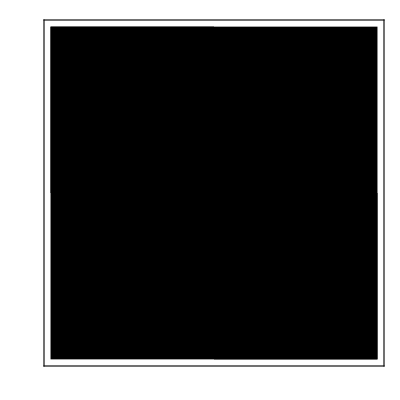
```mathematica
tickopts=ReplacePart[Ticks /. Quiet[AbsoluteOptions[plots[[1]]]],{{1,1,2}->Null,{1,3,2}->Null,{1,5,2}->Null,2->Automatic}];
MyPlotOpts={PlotLabel->None,ImageSize->CalcImgSize[0.3],Ticks->tickopts};
(*ticks=Flatten[Table[{m 10^(v),,{0.005,0.},{-Graphics-,AbsoluteThickness[0.1]}},{v,-5,0,1},{m,0,1,0.1}],1]~Join~
Table[{10^(v),N[10^(v)],{0.01,0.},{-Graphics-,AbsoluteThickness[0.1]}},{v,-5,0,1}];*)
ticks4decomp=Map[ReplacePart[#,{1}->Exp[#[[1]]]]&,tickopts[[1]]];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,12,0.1]
eeFits=eeFits[[{1,3,4}]];
ratio=GetPlotCoordinateRatio[plots[[3]]];
plots4Export=
{Show[plots[[1]],Evaluate@MyPlotOpts],Show[plots[[2]],AxesLabel->{Eps,h2m},PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->0.5][[1]]&,eeFits],AxesLabel->{Eps,EEm},Evaluate@MyPlotOpts,Epilog->Map[PlotFitInLog[#,LabelSize->4,LabelAngle->Automatic,LabelPosition->{Automatic,-.4},BasePlotRatio->ratio, ShowLabel->True][[2]]&,eeFits],PlotRangeClipping->False]
}
```

```mathematica
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_D2.pdf","_h2.pdf","_excess_entropy.pdf"},plots4Export]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10,ShowLabel->True];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.05,YPlotRangeMax->DecompYRange,ShowNegative->True,ReplaceEndByFits->True, ImageSize->DecomposePlotSize,XTicks->ticks4decomp];
EEdecompPlot
```

```mathematica
detInts={{Interval[{0.1,0.4}],1,.6},{Interval[{0.006,0.025}],-.6,.8}};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],Epilog->{Gray,Map[PlotFitInLog[#[[1]],LabelSize->6,LabelAngle->Automatic,BasePlotRatio->ratio,ShowLabel->#[[2]]][[2]]&,Zip[eeFits,{True,True,False}]],Black,Map[AvgDecompInPlot[##,LabelSize->6]&@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits.pdf",Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)],Joined->True,PlotRange->All,PlotStyle->Cyan]],Background->None,ImageSize->1600];
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

### 4 m

```mathematica
basename="hexa_jump_4m";
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/hexapod/Hexapod_tz_jump_4m_fixed.x_x1_d4_e25.d2",1,Thresh->5,EpsRange->{0.001,Infinity},PlotRange->All];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,10,0.01]
ratio=GetPlotCoordinateRatio[plots[[3]]];
plots4Export=
{Show[plots[[1]],Evaluate@MyPlotOpts],Show[plots[[2]],AxesLabel->{Eps,h2m},PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->0.5][[1]]&,eeFits],AxesLabel->{Eps,EEm},Evaluate@MyPlotOpts,Epilog->Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->True][[2]]&,eeFits],PlotRangeClipping->False]
}
```

```mathematica
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_D2.pdf","_h2.pdf","_excess_entropy.pdf"},plots4Export]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10,ShowLabel->True];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold-> 0.1,DeterminismThreshold->0.5, YPlotRangeMax->DecompYRange,RemoveNegative->True, ShowNegative->True, ReplaceEndByFits->True,ImageSize->DecomposePlotSize,XTicks->ticks4decomp];
EEdecompPlot
```

```mathematica
detInts={{Interval[{0.05,0.2}],-.5,1}};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],Epilog->{Gray,Map[PlotFitInLog[#,LabelSize->6,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->True][[2]]&,eeFits],Black,Map[AvgDecompInPlot[##,LabelSize->6]&@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits.pdf",Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)],Joined->True,PlotRange->All,PlotStyle->Cyan]],Background->None,ImageSize->1600];
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

### 8 m

```mathematica
basename="hexa_jump_8m";
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/hexapod/Hexapod_tz_jump_fixed.x_x1_d4_e25.d2",1,Thresh->5,EpsRange->{0.001,Infinity},PlotRange->All];
```

```mathematica
eeFits=FindAllFits[("E" /.tiseandat)[[-1]],LogLinFitFun,10,0.01]
ratio=GetPlotCoordinateRatio[plots[[3]]];
plots4Export=
{Show[plots[[1]],Evaluate@MyPlotOpts],Show[plots[[2]],AxesLabel->{Eps,h2m},PlotRange->{All,{0,6.2}},Evaluate@MyPlotOpts],
Show[plots[[3]],Map[PlotFitInLog[#,ExtendFit->0.5][[1]]&,eeFits],AxesLabel->{Eps,EEm},Evaluate@MyPlotOpts,Epilog->Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->True][[2]]&,eeFits],PlotRangeClipping->False]
}
```

```mathematica
Map[Export[TiseanExportDir<>basename<>#[[1]],#[[2]],Background->None]&,Zip[{"_D2.pdf","_h2.pdf","_excess_entropy.pdf"},plots4Export]]
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10,ShowLabel->True];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold-> 0.05,DeterminismThreshold->0.5, YPlotRangeMax->DecompYRange,ShowNegative->True, RemoveNegative->True, ReplaceEndByFits->True, ImageSize->DecomposePlotSize,XTicks->ticks4decomp];
EEdecompPlot
```

```mathematica
detInts={(*{Interval[{0.003,0.015}],.3,.9},*){Interval[{0.1,0.4}],1,.8}};
ratio=GetPlotCoordinateRatio[EEdecompPlot];
avgDecomp=Map[Prepend[#,GetAvgDecomp[EEdecompData,First[#]]]&,detInts]
plt=Show[EEdecompPlot,Map[PlotFitInLog[#,ExtendFit->.5][[1]]&,eeFits],Epilog->{Gray,Map[PlotFitInLog[#,LabelSize->6,LabelAngle->Automatic,BasePlotRatio->ratio, ShowLabel->True][[2]]&,eeFits],Black,Map[AvgDecompInPlot[##,LabelSize->6]&@@#&,avgDecomp]}];
plt
```

```mathematica
Export[TiseanExportDir<>basename<>"_deltaH-fits.pdf",Show[deltaHplt,ListLogLinearPlot[Map[Zip[dat[[1,All,1]],#]&,("straights"/.aux)],Joined->True,PlotRange->All,PlotStyle->Cyan]],Background->None,ImageSize->1600];
Export[TiseanExportDir<>basename<>"_excess_entropy-decomp.pdf",plt[[1]],Background->None];
```

```mathematica
legend25=TiseanLegend[25]
Export[TiseanExportDir<> "legend25.pdf",legend25,Background->None];
```

### KSG

based on x[1]

```mathematica
files=GetFiles["MIxnyn/hexapod/","*jump*x1-k2_d4*.grouped"]
hexjump12pls=Map[PlotMIScan[#[[1]],#[[2]]]&,Zip[Map[Import,files],files]];
```

```mathematica
tickopts=Ticks/.AbsoluteOptions[hexjump12pls[[1]]];
```

```mathematica
f1[x_]:=Const-Dim Log[x]/.{Dim->1.1,Const->0.2}
f1a[x_]:=Const-Dim Log[x]/.{Dim->1.4,Const->-0.6}
f2[x_]:=Const-Dim Log[x]/.{Dim->1.8,Const->-0.3}
f3[x_]:=Const-Dim Log[x]/.{Dim->1.7,Const->0}
hexjump12plswl={
Show[hexjump12pls[[1]],LogLinearPlot[f1[x],{x,0.03,1},PlotStyle->fittedLineStyle],LogLinearPlot[f1a[x],{x,0.002,0.06},PlotStyle->fittedLineStyle],PlotLabel->None,ImageSize->CalcImgSize[0.4],PlotRange->{{Log[0.0009],1.1},{0,8}},AxesOrigin->{Log[0.0008],0},Ticks->tickopts,PlotRangeClipping->True,
Epilog->{
Inset[Rotate[StyleLabel[f1[ϵ]],-33Degree],{Log[.4],f1[.4]},{Center,-.4}],
Inset[Rotate[StyleLabel[f1a[ϵ]],0Degree],{Log[.005],f1a[.005]},{Left,-.4}]}],
Show[hexjump12pls[[2]],LogLinearPlot[f2[x],{x,0.02,5},PlotStyle->fittedLineStyle],PlotLabel->None,ImageSize->CalcImgSize[.4],
PlotRange->{{Log[0.002],1.1},{0,8}},AxesOrigin->{Log[0.00185],0},Ticks->tickopts,
Epilog->{Inset[Rotate[StyleLabel[f2[ϵ]],-46Degree],{Log[.3],f2[.3]},{Center,-.4}]}],
Show[hexjump12pls[[3]],LogLinearPlot[f3[x],{x,0.02,5},PlotStyle->fittedLineStyle],PlotLabel->None,ImageSize->CalcImgSize[.4],
PlotRange->{{Log[0.002],1.1},{0,8}},AxesOrigin->{Log[0.00185],0},Ticks->tickopts,
Epilog->{Inset[Rotate[StyleLabel[f3[ϵ]],-43Degree],{Log[.3],f3[.3]},{Center,-.5}]}]}
```

```mathematica
Map[Export[MIExportDir<>"hexa_jump_" <> #[[2]] <> "_PI.pdf",#[[1]],Background->None]&,ZipS[hexjump12plswl,{"2m","4m","8m"}]]
```

## AR2 Model of Lorenz

#### AR 2 Analytic MI :

```mathematica
α1=1.991843;
α2=-0.994793;
```

MI - 1

x_(n+1) = a_1 x_n + a_2 x_(n-1) + ϵ_n

MI(X_(n+1):X_n) = 2H(X_n) -H(X_(n+1)X_n)
H(X_n) = 1/2 ln(2 π e ⟨x_n^2⟩) 
⟨x^2⟩ = a_1^2⟨x^2⟩ + a_2^2⟨x^2⟩ + ⟨ϵ^2⟩
β = ⟨x^2⟩ =σ^2/(1-a_1^2-a_2^2)
σ^2 = ⟨ϵ^2⟩
H(X_n) = 1/2 ln(2 π e  β) 
H(X_(n+1)X_n) = 1/2 ln((2 π e )^2 |K|)
K=(β | ⟨x_(n+1)x_n⟩
⟨x_(n+1)x_n⟩ | β)
⟨x_(n+1)x_n⟩ = a_1 ⟨x_n^2⟩ + a_2⟨x_(n-1)x_n⟩
⟨x_(n+1)x_n⟩ = a_1/(1-a_2)β = r β
r= a_1/(1-a_2)

H(X_(n+1)X_n) = 1/2 ln((2 π e )^2 β^2(1-r^2))
MI(X_(n+1):X_n) = 1/2 ln (1-r^2) = 1/2 ln(1-(a_1/(1-a_2))^2)

```mathematica
ar2Pi1=-1/2 Log[1-(α1/(1-α2))^2]
```

2.91204

```mathematica
(α1/(1-α2))
```

MI-2

MI(X_(n+1)X_n:X_(n-1)X_(n-2)) = 2H(X_(n+1)X_n) -H(X_(n+1)X_n X_(n-1)X_(n-2))

H(X_(n+1)X_n)= 1/2 ln((2 π e )^2 β^2(1-r^2))

H(X_(n+1)X_n X_(n-1)X_(n-2)) = 1/2 ln((2 π e )^4 |K|)

K=(β | r β | r_2 β | r_3 β
r β | β | r β | r_2 β
r_2 β | r β | β | r β
r_3 β | r_2 β | r β | β) 
r= a_1/(1-a_2)

⟨x_(n+1)x_(n-1)⟩ = a_1 ⟨x_n x_(n-1)⟩ + a_2⟨x_(n-1)^2⟩=a_1 r β + a_2 β = β r_2
r_2= a_1 r + a_2
⟨x_(n+1)x_(n-2)⟩ = a_1 ⟨x_n x_(n-2)⟩ + a_2⟨x_(n-1)x_(n-2)⟩=a_1 r_2 β+ a_2 r β = β r_3
r_(3 =)a_1 r_2+ a_2 r

```mathematica
K=β{{1,r,r2,r3},{r,1,r,r2},{r2,r,1,r},{r3,r2,r,1}};
K//MatrixForm
rules={β->σ^2/(1-a1^2-a2^2), r3-> a1 r2 + a2 r, r2->a1 r + a2, r-> a1/(1-a2)}
Det[K]
H4=(Det[K]//. rules)//FullSimplify
H2 = β^2(1-r^2)//. rules//FullSimplify
H2^2/H4 // FullSimplify
```

MI(X_(n+1)X_n:X_(n-1)X_(n-2))=1/2 ln1/((1+a_2)^2  ((a_2-1)^2-a_1^2))

```mathematica
ar2Pi2=1/2 Log[H2^2/H4 /.{a1->α1,a2->α2}]
```

7.47925

2 - step delay (delay=1)
Iterate quation and calc correlation:

```mathematica
Clear[s]
rules2 = {s->a1^2 + a2 + a2 a1 r, β -> σ^2(1+a1^2)/(1-a1^4-a2^2-a1^2 a2^2)}
```

{s→a1^2+a2+a1 a2 r,β→((1+a1^2) σ^2)/(1-a1^4-a2^2-a1^2 a2^2)}

{s→a1^2+a2+a1 a2 r,β→((1+a1^2) σ^2)/(1-a1^4-a2^2-a1^2 a2^2)}

```mathematica
ar2Pi1d2=1/2 Log[1/(1-s^2) //.Flatten[{rules,rules2,a1->α1,a2->α2}]]
```

N - step iteration

```mathematica
x[0]=xn
x[-1]=xm
x[n_]:=a1 x[n-1] + a2 x[n-2]
```

xn

xm

Correlation coefficient: s=c1+ c2 r with r=a_1/(1-a_2) 
where c_1 are the coeficients for x_n and c_2 are the coefficients for x_(n-1)

```mathematica
corr[x_] :=  Coefficient[Collect[x,xn],xn] + Coefficient[Collect[x,xm],xm]r /.r-> a1/(1-a2)
```

```mathematica
Map[corr[x[#]]&,{1,2,3,4,6,10}]// FullSimplify
```

{a1/(1-a2),a1^2/(1-a2)+a2,(a1 (-a1^2+(-2+a2) a2))/(-1+a2),(-a1^4+a1^2 (-3+a2) a2+(-1+a2) a2^2)/(-1+a2),(-a1^6+a1^4 (-5+a2) a2+3 a1^2 (-2+a2) a2^2+(-1+a2) a2^3)/(-1+a2),(-a1^10+a1^8 (-9+a2) a2+7 a1^6 (-4+a2) a2^2+(-1+a2) a2^5+5 a1^2 a2^4 (-3+2 a2)+5 a1^4 a2^3 (-7+3 a2))/(-1+a2)}

```mathematica
ar2Pi1d[d_]:=1/2 Log[1/(1-corr[x[d]]^2) /.{a1->α1,a2->α2}];
```

```mathematica
Map[{#,ar2Pi1d[#]}&,Table[x,{x,1,10}]]
```

{{1,2.91204},{2,2.22167},{3,1.81968},{4,1.53637},{5,1.31855},{6,1.14252},{7,0.995632},{8,0.870342},{9,0.761785},{10,0.666643},{11,0.582549},{12,0.507762},{13,0.440958},{14,0.381115},{15,0.327425},{16,0.279238},{17,0.236029},{18,0.197364}}

The correlation coefficients in the matrix are the delayed correlations given by corr[x[i]]

```mathematica
row = {1,corr[x[1]],corr[x[2]],corr[x[3]],corr[x[2]],corr[x[1]]}// FullSimplify;
K2=β Map[Take[RotateRight[row,#],4]&,{0,1,2,3}];
K2//MatrixForm
```

(β | (a1 β)/(1-a2) | (a1^2/(1-a2)+a2) β | (a1 (-a1^2+(-2+a2) a2) β)/(-1+a2)
(a1 β)/(1-a2) | β | (a1 β)/(1-a2) | (a1^2/(1-a2)+a2) β
(a1^2/(1-a2)+a2) β | (a1 β)/(1-a2) | β | (a1 β)/(1-a2)
(a1 (-a1^2+(-2+a2) a2) β)/(-1+a2) | (a1^2/(1-a2)+a2) β | (a1 β)/(1-a2) | β)

(β | (a1 β)/(1-a2) | (a1^2/(1-a2)+a2) β | (a1 (-a1^2+(-2+a2) a2) β)/(-1+a2)
(a1 β)/(1-a2) | β | (a1 β)/(1-a2) | (a1^2/(1-a2)+a2) β
(a1^2/(1-a2)+a2) β | (a1 β)/(1-a2) | β | (a1 β)/(1-a2)
(a1 (-a1^2+(-2+a2) a2) β)/(-1+a2) | (a1^2/(1-a2)+a2) β | (a1 β)/(1-a2) | β)

```mathematica
H4=(Det[K2])//FullSimplify
H2 = β^2(1-(corr[x[1]])^2)//FullSimplify
H2^2/H4 // FullSimplify
1/2 Log[H2^2/H4 /.{a1->α1,a2->α2}]
```

7.47925

1/((-a1^2+(-1+a2)^2) (1+a2)^2)

(1-a1^2/(-1+a2)^2) β^2

((-a1^2+(-1+a2)^2)^3 (1+a2)^2 β^4)/(-1+a2)^4

((-a1^2+(-1+a2)^2)^3 (1+a2)^2 β^4)/(-1+a2)^4

(1-a1^2/(-1+a2)^2) β^2

1/((-a1^2+(-1+a2)^2) (1+a2)^2)

7.47925

```mathematica
ar2Pi2d[d_]:= Module[{row,K,r},
row = {1,corr[x[d]],corr[x[2d]],corr[x[3d]],corr[x[2d]],corr[x[1d]]}// FullSimplify;
K=Map[Take[RotateRight[row,#],4]&,{0,1,2,3}];
r=FullSimplify[Simplify[(1-(corr[x[d]])^2)^2]/(Det[K]//Simplify)];
1/2 Log[r /.{a1->α1,a2->α2}]
]
```

```mathematica
dat=Map[{#,ar2Pi2d[#]}&,Table[x,{x,1,10}]]
```

#### Values

```mathematica
ar2Pi2dValues=Map[Rule @@ #&,{{1,7.479252575358022},{2,6.399409360532621},{3,5.665917874368521},{4,5.123104944326739},{5,4.695401920363092},{6,4.343788221912529},{7,4.048648310733302},{8,3.788140099593134},{10,3.358748352585658}}]
```

{1→7.47925,2→6.39941,3→5.66592,4→5.1231,5→4.6954,6→4.34379,7→4.04865,8→3.78814,10→3.35875}

#### AR2 with D2 - Delay 1

```mathematica
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/lorenz/ar2-lorenz_d1.d2",1,Thresh->2,EpsRange->{0.001,Infinity},PlotRange->{All,All}];
GraphicsRow[plots]
ar2plotsd1=plots;
```

```mathematica
Export[TiseanExportDir<>"ar2lorenz-d1_all.pdf",%,Background->None];
```

```mathematica
value=ar2Pi1d[1];
Show[ar2plotsd1[[3]],LogLinearPlot[value,{x,0.001,50},PlotStyle->Directive[Black,Dashed,AbsoluteThickness[.5]]],
LogLinearPlot[Const-Dim Log[x]/.{Dim->0,Const->1/. ar2Pi2dValues},{x,0.001,50},PlotStyle->Directive[Black,Dashed,AbsoluteThickness[.5]]],
PlotRange->{Automatic,{0,9}},AxesOrigin->{Log[0.001],0}, PlotLabel->None,ImageSize->CalcImgSize[0.4],Epilog->{Inset[StyleLabel[Round[ar2Pi1d[1],0.01]],{Log[5],3.5}],Inset[StyleLabel[Round[1/. ar2Pi2dValues,0.01]],{Log[1],8}]}]
```

```mathematica
Export[TiseanExportDir<>"ar2lorenz-delay1_excess_entropy.pdf",%,Background->None];
```

```mathematica
Export[TiseanExportDir<>"ar2lorenz-delay1_D2.pdf",Show[ar2plotsd1[[1]],ImageSize->CalcImgSize[0.4],PlotLabel->None,PlotRange->{All,{0,10}}],Background->None];
```

```mathematica
Export[TiseanExportDir<>"ar2lorenz-delay1_H2.pdf",Show[ar2plotsd1[[2]],ImageSize->CalcImgSize[0.4],PlotLabel->None, PlotRange->{All,{0,10}}],Background->None];
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.1, DeterminismThreshold->0.5,RemoveNegative->True,ShowNegative->True,  ReplaceEndByFits->True,YPlotRangeMax->12, ImageSize->DecomposePlotSize];
EEdecompPlot
```

```mathematica
Export[TiseanExportDir<>"ar2lorenz-delay1_excess_entropy_decomp.pdf",%,Background->None];
```

#### AR2 with D2 - Delay 10

```mathematica
{plots,tiseandat}=TiseanD2PlotsAndData["tisean/lorenz/ar2-lorenz_d10.d2",1,Thresh->2,EpsRange->{0.01,Infinity},PlotRange->{All,All}];
GraphicsRow[plots]
ar2plotsd10=plots;
```

```mathematica
value=ar2Pi1d[10];
Show[ar2plotsd10[[3]],LogLinearPlot[value,{x,0.01,50},PlotStyle->Directive[Black,Dashed,AbsoluteThickness[.5]]],
LogLinearPlot[Const-Dim Log[x]/.{Dim->0,Const->10/. ar2Pi2dValues},{x,0.01,50},PlotStyle->Directive[Black,Dashed,AbsoluteThickness[.5]]],
PlotRange->{All,{0,5}}, PlotLabel->None,ImageSize->CalcImgSize[.4],Epilog->{Inset[StyleLabel[Round[ar2Pi1d[10],0.01]],{Log[20],1}],Inset[StyleLabel[Round[10/. ar2Pi2dValues,0.01]],{Log[10],3.8}]}]
```

```mathematica
Export[TiseanExportDir<>"ar2lorenz-delay10_excess_entropy.pdf",%,Background->None];
```

```mathematica
Export[TiseanExportDir<>"ar2lorenz-delay10_D2.pdf",Show[ar2plotsd10[[1]],ImageSize->CalcImgSize[.4],PlotLabel->None,PlotRange->{All,{0,10}}],Background->None];
```

```mathematica
Export[TiseanExportDir<>"ar2lorenz-delay10_H2.pdf",Show[ar2plotsd10[[2]],ImageSize->CalcImgSize[.4],PlotLabel->None, PlotRange->{All,{0,10}}],Background->None];
```

```mathematica
{dat,fits,deltaHplt}=FitDeltaHs[plots,tiseandat,MinFitLength->10];
```

```mathematica
{EEdecompPlot,EEdecompData,aux}=DecomposeAndPlotExcessEntropy[dat,fits,DeltaHFlatThreshold->0.1, DeterminismThreshold->0.5,RemoveNegative->True,ShowNegative->True,  ReplaceEndByFits->True,YPlotRangeMax->8, ImageSize->DecomposePlotSize];
EEdecompPlot
```

```mathematica
Export[TiseanExportDir<>"ar2lorenz-delay10_excess_entropy_decomp.pdf",%,Background->None];
```

### KSG

```mathematica
fs={"MIxnyn/lorenz/ar2-lorenzk20_d1.pi.grouped","MIxnyn/lorenz/ar2-lorenzk20_d10.pi.grouped"};
plsmiar2=Map[PlotMIScan[#[[1]],#[[2]],PlotRange->{{0.001,Automatic},{0,Automatic}}]&,Zip[Map[Import,fs],fs]];
plsmiar2wn=Map[Show[#[[1]],LogLinearPlot[#[[2]],{x,0.001,20},PlotStyle->fittedLineStyle],LogLinearPlot[#[[3]],{x,0.001,20},PlotStyle->fittedLineStyle]]&,Zip3[plsmiar2,Map[ar2Pi1d,{1,10}],{1,10}/.ar2Pi2dValues]]
```

```mathematica
Show[plsmiar2wn[[1]],ImageSize->200,PlotLabel->None, PlotRange->{{Log[0.001],Automatic},{0,8.5}},
Epilog->{Inset[StyleLabel[Round[ar2Pi1d[1],0.01]],{Log[5],3.5}],Inset[StyleLabel[Round[1/. ar2Pi2dValues,0.01]],{Log[5],8}]}]
```

```mathematica
Export[MIExportDir<>"ar2lorenz-delay1_MI.pdf",%,Background->None];
```

```mathematica
Show[plsmiar2wn[[2]],ImageSize->200,PlotLabel->None,PlotRange->{{Log[0.001],Automatic},{0,4}},
Epilog->{Inset[StyleLabel[Round[ar2Pi1d[10],0.01]],{Log[.5],1}],Inset[StyleLabel[Round[10/. ar2Pi2dValues,0.01]],{Log[3],3.7}]}]
```

```mathematica
Export[MIExportDir<>"ar2lorenz-delay10_MI.pdf",%,Background->None];
```